{{-3,-1},{{-1,1},{1,0}}}

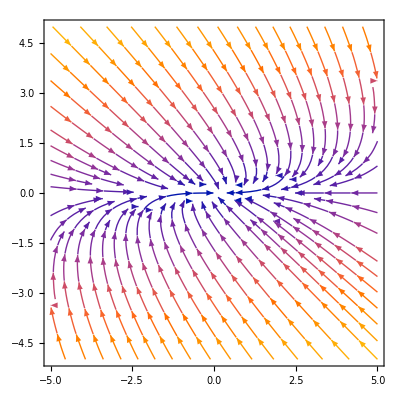

```mathematica
(* Задача 1 *)
A={{-1,2},{0,-3}};
NullSpace[A];
Eigensystem[A]
StreamPlot[A.{x,y},{x,-5,5},{y,-5,5}]
```

{{-6,2},{{-3,5},{1,1}}}

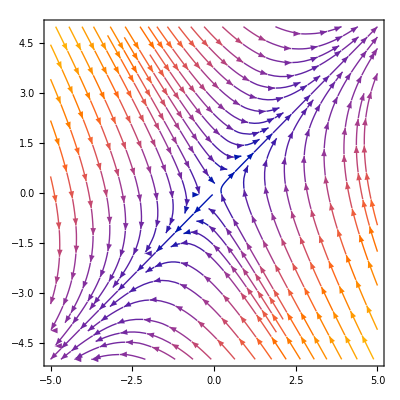

```mathematica
B={{-1,3},{5,-3}};
NullSpace[B];
Eigensystem[B]
StreamPlot[B.{x,y},{x,-5,5},{y,-5,5}]
```

```mathematica
(* Задача 2 *)
dimensionalMatrix={
(*    t  V  D γ s sin x b  a *)
(*M*){0,0,0,0,1,1,1,1,0},
(*L*){0,3,3,0,-3,-3,-3,-3,0},
(*T*){1,0,-1,0,0,0,0,0,-1}
};
Max@Dimensions@dimensionalMatrix - Length@NullSpace@dimensionalMatrix;
(* dsdt[s_,x_]:=1-s-(a s)/(b+s)x
dxdt[s_,x_]:=((a s)/(b+s)-1)x *)
FindTrajectories[a_,b_]:=(
dsdt[s_,x_,t_]=1-s[t]-(a s[t])/(b+s[t])x[t];
dxdt[s_,x_,t_]=((a s[t])/(b+s[t])-1)x[t];
solveEquation[x0_,s0_,tMin_,tMax_]:=
NDSolveValue[{s'[t]==dsdt[s,x,t],x'[t]==dxdt[s,x,t],x[0]==x0,s[0]==s0} ,{s,x},{t,tMin,tMax}];
n=3;
startingPoints=Flatten[Table[N@{i/n,j/n},{i,0,n},{j,0,n}],1];
T=10;
solutions=solveEquation[#⟦1⟧,#⟦2⟧,0,T]&/@startingPoints;
Transpose@Table[Through[#[τ]]&/@solutions,{τ,0,T}]
)
dVec={1-s-(a s)/(b+s)x,(a s)/(b+s)-1};
j=Grad[dVec,{s,x}];
stability[linearization_]:=If[Max@(Re/@Eigenvalues@linearization)<0,"stable","unstable"]
stabilityString[linearization_,equilibriumPoint_]:=StringTemplate["The equilibrium point with coords `1` is `2`"][equilibriumPoint,stability@linearization]
```

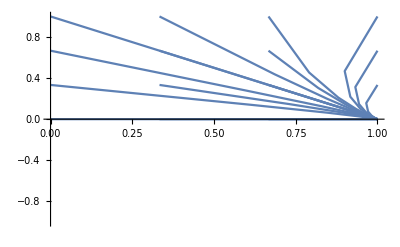

The equilibrium point with coords {1, 0} is stable

```mathematica
a=0.5;
b=1;
points=FindTrajectories[a,b];
Show[
ListLinePlot/@points
]
spLinearization=j/.{s->1,x->0};
stabilityString[spLinearization,{1,0}]
```

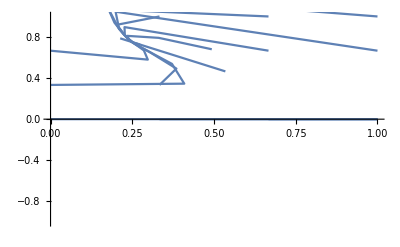

The equilibrium point with coords {1, 0} is stable

The equilibrium point with coords {0.25, 0.75} is stable

```mathematica
a=5;
b=1;
points=FindTrajectories[a,b];
Show[
ListLinePlot/@points
]
fpLinearization=j/.{s->1,x->0};
stabilityString[fpLinearization,{1,0}]
secondPoint=FindRoot[#==0&/@dVec,{{s,0.3},{x,0.7}}];
spLinearization=j/.secondPoint;
stabilityString[spLinearization,{s,x}/.secondPoint]
```

```mathematica
#==0&/@dVec
```

{1-s-(0.5 s x)/(1+s)==0,-1+(0.5 s)/(1+s)==0}